```mathematica
Ω=({{ω1, -J, 0}, {-J, ω2, -J}, {0, -J, ω3}});
Ωsim = Ω/.{ω1->ω0,ω2->ω0,ω3->ω0};
```

```mathematica
Eigensystem[Ωsim]
```

{{ω0,-√2 J+ω0,√2 J+ω0},{{-1,0,1},{1,√2,1},{1,-√2,1}}}

```mathematica
ωC =Eigenvalues[Ωsim][[2]];
ωS=Eigenvalues[Ωsim][[1]];
ωAS = Eigenvalues[Ωsim][[3]];

aC =Eigenvectors[Ωsim][[2]];
aS=Eigenvectors[Ωsim][[1]];
aAS = Eigenvectors[Ωsim][[3]];
```

```mathematica
ω1[μ_]:=ω0 + d1×μ + d2/2 μ^2 + δ1;
ω2[μ_]:=ω0 + D1×μ + D2/2 μ^2 + δ2;
ω3[μ_]:=ω0 + d1×μ + d2/2 μ^2+ δ3;
```

```mathematica
Ω=({{ω1[μ], -J[μ], 0}, {-J[μ], ω2[μ], -J[μ]}, {0, -J[μ], ω3[μ]}});
```

```mathematica
d1=454.66; (* FSR *)
d2=-0.01533;(*-8.08×10^-3;*) (* GVD *)
D1=454.66*0.9945/2;
D2=-0.01533;
J[μ_]=3.43343343/(√2);(* Splitting *)
```

```mathematica
Definitions
H[μ_,δ1_,δ2_,δ3_]:=({{(ω1[μ,δ1]-d1×μ), -J[μ], 0}, {-J[μ], (ω2[μ,δ2]-d1×μ), -J[μ]}, {0, -J[μ], (ω3[μ,δ3]-d1×μ)}});
ω1[μ_,δ1_]:=ω0 +d1×μ + d2/2 μ^2+δ1;
ω2[μ_,δ2_]:=ω0 + D1×(2μ) + D2/2(2μ)^2+δ2;
ω3[μ_,δ3_]:=ω0+d1×μ + d2/2 μ^2 +δ3;
d1=454.66; (* FSR *)
d2=-0.01533;(*-8.08×10^-3;*) (* GVD *)
D1=454.66*0.9945/2;
D2=-0.01533;
J[μ_]:=3.43343343/(√2);(* Splitting *)
(*J[μ_]:= E^(0.02071371*μ + 1.09238286) + 0.65560241;*)
ω0=0;
```

Definitions

```mathematica
Eigensystem[Ω];
```

#### Eigenproblem

```mathematica
sortedEig[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3]=Module[{vals,vecs,pairs,fixSign},
fixSign[v_]:=If[Re[v[[1]]]<0,-v,v];
{vals,vecs}=Eigensystem[H[μ,δ1,δ2,δ3]];
vecs=fixSign/@vecs;
pairs=Transpose[{vals,vecs}];
SortBy[pairs,First]];
```

```mathematica
ωS[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3][[1,1]];  (*smallest eigenvalue*)
bS[μ_,δ1_,δ2_,δ3_]:=Normalize[sortedEig[μ,δ1,δ2,δ3][[1,2]]];

ωC[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3][[2,1]];
bC[μ_,δ1_,δ2_,δ3_]:=Normalize[sortedEig[μ,δ1,δ2,δ3][[2,2]]];

ωAS[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3][[3,1]];  (*largest eigenvalue*)
bAS[μ_,δ1_,δ2_,δ3_]:=Normalize[sortedEig[μ,δ1,δ2,δ3][[3,2]]];
```

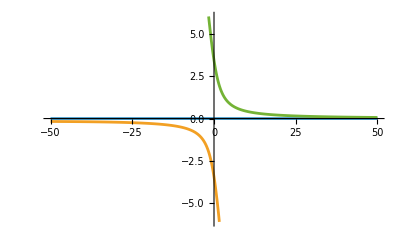

```mathematica
Plot[{ωC[μ,0,0,0] - ωC[μ,0,0,0],ωS[μ,0,0,0] - ωC[μ,0,0,0], ωAS[μ,0,0,0]- ωC[μ,0,0,0]},{μ,-50,50}]
```